```mathematica
im=Import["/home/adam/Music/yt/charbhoy.mp3"];
```

```mathematica
im
```

```mathematica
3*60+52
```

232

```mathematica
ad=AudioData[im];
```

```mathematica
If[adpm={ad[[1]]-ad[[2]],ad[[1]]+ad[[2]]}]
```

{2,1440000}

```mathematica
adpp={ad[[1]]+ad[[2]],ad[[1]]+ad[[2]]}/Sqrt[2];4;
```

```mathematica
Export["/home/adam/Music/yt/char-rff2.mp3",a];
```

```mathematica
adpm={ad[[1]]-ad[[2]],ad[[1]]+ad[[2]]};
```

```mathematica
a=Audio[rff,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
```

```mathematica
a
```

```mathematica
adf=Re@Fourier[Fourier[ad[[1]]]];4;
```

```mathematica
Max@Abs@Im@Fourier[Reverse[rf]]
```

0.00210668

```mathematica
f=Sqrt[2]*Re@Fourier[ad[[1]]];4;
ff=Re@Fourier[f];4;
```

```mathematica
a=Audio[ff,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-refref.mp3",a];
```

```mathematica
f=(Exp[I 2Pi Random[]]&/@Range[l])*Fourier[ad[[1]]];4;
ff=Re@Fourier[f];4;
```

```mathematica
a=Audio[ff,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-randphase.mp3",a];
```

```mathematica
f=Fourier[ad[[1]]];4;
fflat=f*(Range[l/2]~Join~Reverse[Range[l/2]]);4;
rfflat=Reverse[fflat[[;;l/2]]]~Join~Reverse[fflat[[l/2+1;;]]];4;
rf=rfflat/(Range[l/2]~Join~Reverse[Range[l/2]]);4;
rfrf=Re@Fourier[Reverse[rf]];4;
```

```mathematica
a=Audio[rfrf,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-rfrf-full.mp3",a];
```

```mathematica
l=Length[f]
```

11119104

```mathematica
f=Fourier[ad[[1]]];4;
fflat=f*(Range[l/2]~Join~Reverse[Range[l/2]]);4;
cut=35*10^5;
rfflat=Reverse[fflat[[;;cut]]]~Join~
Reverse[fflat[[cut+1;;l-cut]]]~Join~
Reverse[fflat[[l-cut+1;;]]];4;
rf=rfflat/(Range[l/2]~Join~Reverse[Range[l/2]]);4;
rfrf=Re@Fourier[Reverse[rf]];4;
```

```mathematica
a=Audio[rfrf,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-rfrf-cut.mp3",a];
```

```mathematica
rf=Reverse[f[[;;cut]]]~Join~
Reverse[f[[cut+1;;l-cut]]]~Join~
Reverse[f[[l-cut+1;;]]];4;
```

```mathematica
rff=Re@Fourier[Reverse[rf]];4;
```

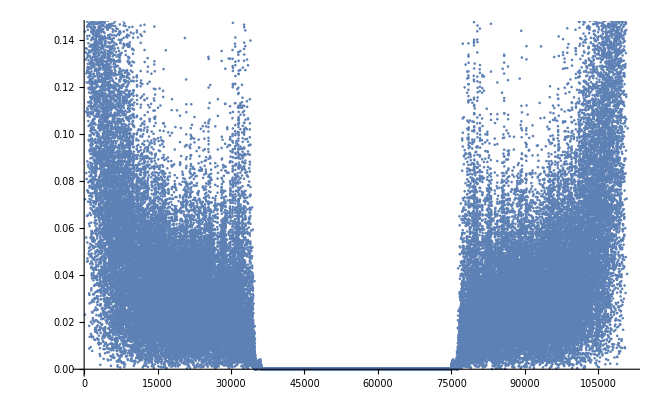

```mathematica
Table[Abs[rf[[i]]],{i,1,l,100}]//ListPlot
```

```mathematica
Divisors[l]
```

{1,2,3,4,6,8,9,12,16,18,19,24,32,36,38,48,57,64,72,76,96,114,127,128,144,152,171,192,228,254,256,288,304,342,381,384,456,508,512,576,608,684,762,768,912,1016,1143,1152,1216,1368,1524,1536,1824,2032,2286,2304,2413,2432,2736,3048,3648,4064,4572,4608,4826,4864,5472,6096,7239,7296,8128,9144,9652,9728,10944,12192,14478,14592,16256,18288,19304,21717,21888,24384,28956,29184,32512,36576,38608,43434,43776,48768,57912,65024,73152,77216,86868,87552,97536,115824,146304,154432,173736,195072,231648,292608,308864,347472,463296,585216,617728,694944,926592,1235456,1389888,1853184,2779776,3706368,5559552,11119104}

```mathematica
l/4826
```

2304

```mathematica
chunks=Partition[ad[[1]],4826];4;
```

```mathematica
chunk=chunks[[100]];4;
f=Fourier[chunk];4;
ll=4826;
fflat=f*(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
cut=1520;
rfflat=Reverse[fflat[[;;cut]]]~Join~
Reverse[fflat[[cut+1;;ll-cut]]]~Join~
Reverse[fflat[[ll-cut+1;;]]];4;
rf=rfflat/(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
rfrf=Re@Fourier[Reverse[rf]];4;
```

```mathematica
ll/3.
```

1608.67

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

```mathematica
rfrf={};
Table[chunk=chunks[[i]];4;
f=Fourier[chunk];4;
ll=4826;
fflat=f*(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
cut=1520;
rfflat=Reverse[fflat[[;;cut]]]~Join~
Reverse[fflat[[cut+1;;ll-cut]]]~Join~
Reverse[fflat[[ll-cut+1;;]]];4;
rf=rfflat/(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
rfrf=Append[rfrf,Reverse[Re@Fourier[Reverse[rf]]]];4;,{i,1,Length[chunks]}];4;
```

```mathematica
a=Audio[Flatten[rfrf],"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-rfrf-dice-rev.mp3",a];
```

```mathematica
rfrf//Dimensions
```

{2304,4826}

```mathematica
rfrf={};
Table[chunk=chunks[[i]];4;
f=Fourier[chunk];4;
ll=4826;
fflat=f*(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
cut=100;
rfflat=Reverse[fflat[[;;cut]]]~Join~
Reverse[fflat[[cut+1;;ll-cut]]]~Join~
Reverse[fflat[[ll-cut+1;;]]];4;
rf=rfflat/(Range[ll/2]~Join~Reverse[Range[ll/2]]);4;
rfrf=rfrf~Join~(Re@Fourier[Reverse[rf]]);4;,{i,1,Length[chunks]}];4;
```

```mathematica
a=Audio[rfrf,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-rfrf-dice100.mp3",a];
```

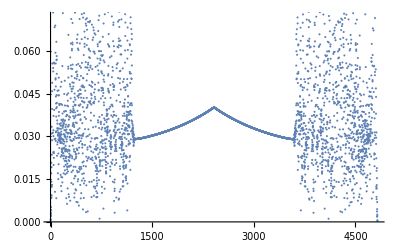

```mathematica
ListPlot[Abs@fflat]
```

```mathematica
rfrf={};
Table[chunk=chunks[[i]];4;
f=Fourier[chunk];4;
ll=4826;

cut=200;
rf=Reverse[f[[;;cut]]]~Join~
Reverse[f[[cut+1;;ll-cut]]]~Join~
Reverse[f[[ll-cut+1;;]]];4;

rfrf=rfrf~Join~(Re@Fourier[Reverse[rf]]);4;,{i,1,Length[chunks]}];4;
```

```mathematica
a=Audio[rfrf,"Real32",Appearance->Automatic,AudioOutputDevice->Automatic,MetaInformation-><|"ID3v2"-><|"EncodingSettings"->"Lavf53.21.1"|>|>,SampleRate->48000,SoundVolume->1];
Export["/home/adam/Music/yt/char-rfrf-dice200-unflat.mp3",a];
```